## RNN Sequence 10

```mathematica
loadTimeSeriesResampled=Import["C:\\Users\\kylem\\Documents\\GitHub\\2019-WSS\\Final Project\\Drafts\\kyle\\LoadtimeseriesResampled.wxf"];
```

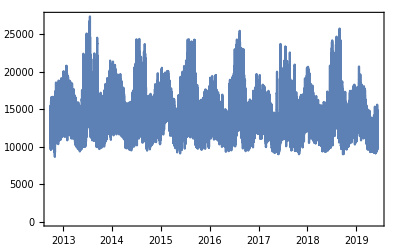

```mathematica
DateListPlot[loadTimeSeriesResampled]
```

```mathematica
data=loadTimeSeriesResampled//Normal;
```

```mathematica
values=QuantityMagnitude@data[[All,2]];keysp=Partition[values,96,1];valuesp = values[[97;;]];
```

```mathematica
threaddata=Thread[Table[ArrayReshape[keysp[[i]],{1,96}]->valuesp[[i]],{i,1,Length@valuesp}]];
```

```mathematica
Length@data
```

58680

```mathematica
58680
```

```mathematica
Length@threaddata
```

58584

```mathematica
{trainingdata,testdata}=TakeDrop[threaddata,45000];
```

```mathematica
rnn=NetChain[
{ConvolutionLayer[100,6,"Interleaving"->True],
Ramp,
ConvolutionLayer[100,6,"Interleaving"->True],
Ramp,
ConvolutionLayer[10,6,"Interleaving"->True],
Ramp,
GatedRecurrentLayer[32,"Dropout"->{"VariationalInput"->0.3},"Input"->{"Varying",10}],GatedRecurrentLayer[64,"Dropout"->{"VariationalInput"->0.3}],GatedRecurrentLayer[64,"Dropout"->{"VariationalInput"->0.3}],SequenceLastLayer[],LinearLayer[128],Ramp,LinearLayer[1]},"Output"->"Scalar"]
```

NetChain[<>]

```mathematica
trainednet=NetTrain[rnn,trainingdata,All,ValidationSet->testdata,BatchSize->800,Method-> "ADAM",MaxTrainingRounds->100]
```

NetTrain::nettinf1: Could not automatically infer types for input and outputs of partially specified net NetChain[«13»]. Please specify shapes for the input and/or output ports of the net before calling NetTrain.

NetTrain::nfspec: Cannot train net: parameter "KernelSize" of first layer is not fully specified.

$Failed

```mathematica
AssociationMap[ PredictorMeasurements[
Predict[trainingdata,Method->#,PerformanceGoal->"DirectTraining"],testdata, "MeanSquare"]&,{"RandomForest"}]
```

```mathematica
SeedRandom[111];rsample=RandomSample[testdata,2]
```

```mathematica
trainednet[rsample[[2,1]]]
```

```mathematica
sobj=NetStateObject[trainednet]
```

```mathematica
tvalues=Table[trainednet[testdata[[i,1]]],{i,1,Length@testdata}]
```

```mathematica
results=Union@Flatten@NestList[Drop[Join[#,{trainedNet[#]}],1]&,testdata[[1,1]],100]
```

```mathematica
ListPlot[{testdata[[1;;1000,2]],results}]
```